```mathematica
If[x<34,If[x<17,A,B],If[x<82,C,D]]
x=RandomReal[{1,106},20];
f/@m
```

If[{72.1789,59.8022,80.6419,75.1498,38.7675,11.2846}<34,If[x<17,A,B],If[x<82,C,D]]

{C,D,C,D,C,C,D,C,C,C,D,D,A,C,C,D,C,B,A,C}

```mathematica
x=17
```

17

```mathematica
mat=SparseArray[{i_,i_}->1,{5,5}]
```

SparseArray[…]

```mathematica
MatrixForm[mat]
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

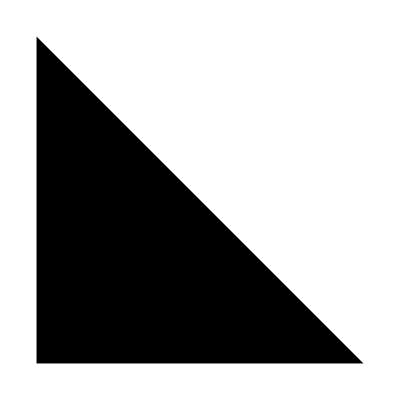

```mathematica
Graphics[Triangle[{{0,0},{0,1},{1,0}}]]
```



```mathematica
Graphics[Circle[]]
```



```mathematica
Graphics[Disk[]]
```

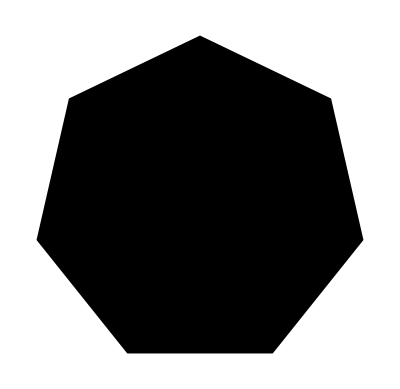

```mathematica
Graphics[RegularPolygon[7]]
```


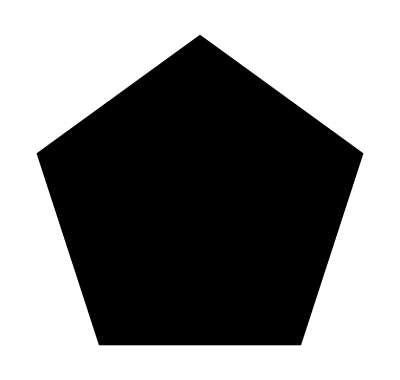
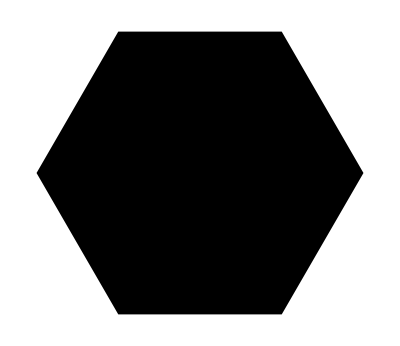
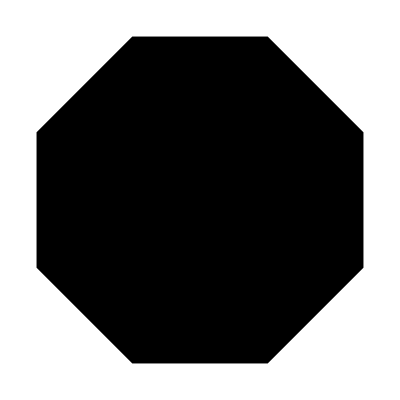
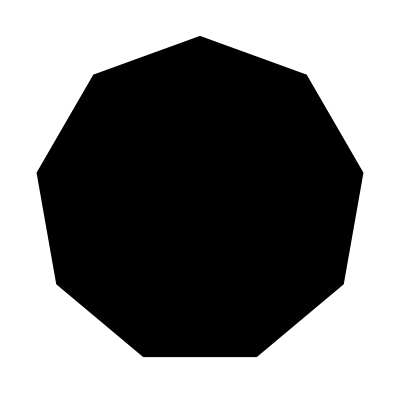
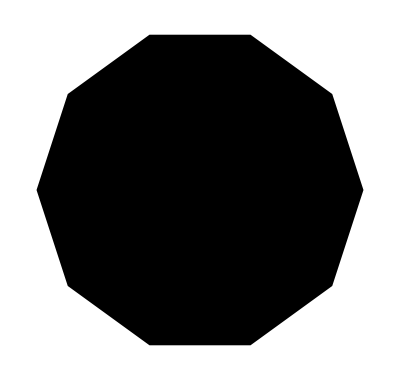
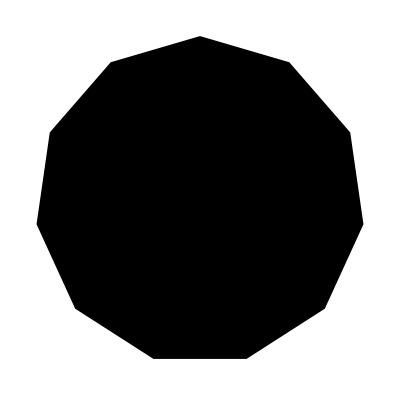
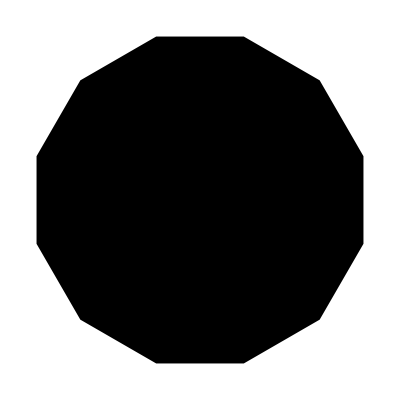
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[RegularPolygon[n]],{n,4,12}]
```

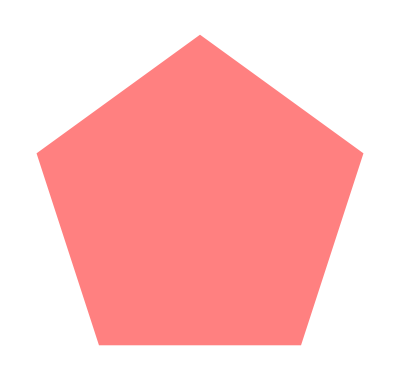

```mathematica
Graphics[Style[RegularPolygon[5],Pink]]
```

```mathematica
Graphics3D[Sphere[]]
```

-Graphics3D-

```mathematica
{Graphics3D[Cone[]],Graphics3D[Cylinder[]]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Graphics3D[Style[Sphere[],Blue]]
```

-Graphics3D-



```mathematica
Graphics[RegularPolygon[3]]
```

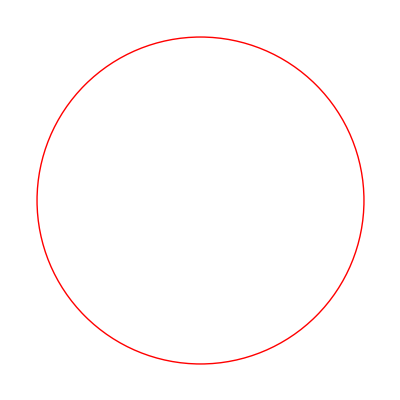

```mathematica
Graphics[Style[Circle[],Red]]
```

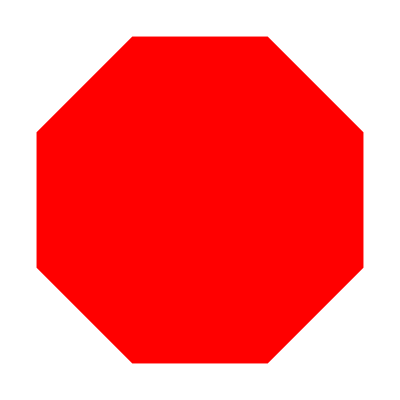

```mathematica
Graphics[Style[RegularPolygon[8],Red]]
```

```mathematica
Table[Hue[x],{x,0,1,.1}]
```

{Hue[0.],Hue[0.1],Hue[0.2],Hue[0.30000000000000004],Hue[0.4],Hue[0.5],Hue[0.6000000000000001],Hue[0.7000000000000001],Hue[0.8],Hue[0.9],Hue[1.]}

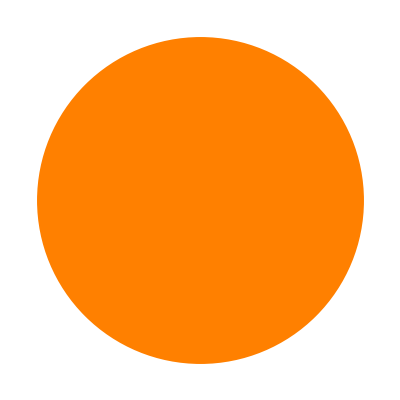

```mathematica
Graphics[Style[Disk[],Orange]]
```

```mathematica
f[x_]:=Graphics[[Disk[],[Hue[x]]]]
x=Range[0,1,.1]
f/@x
```

Syntax::sntxf: "Graphics⟦Disk[]," cannot be followed by "[Hue[x]]⟧".

Syntax::sntxf: "Graphics⟦Disk[]," cannot be followed by "[Hue[x],{x,0,1,.1}]⟧".

```mathematica
Hue[.1]
```

Hue[0.1]

```mathematica
x=Range[0,1,.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}


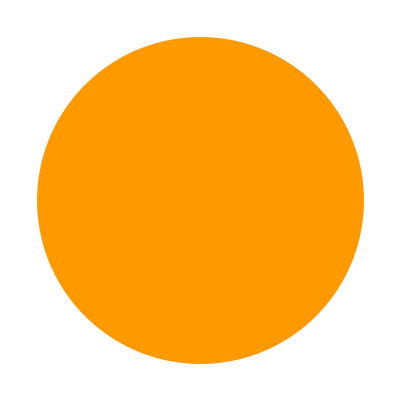
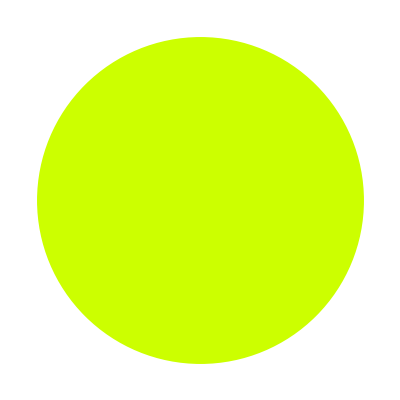
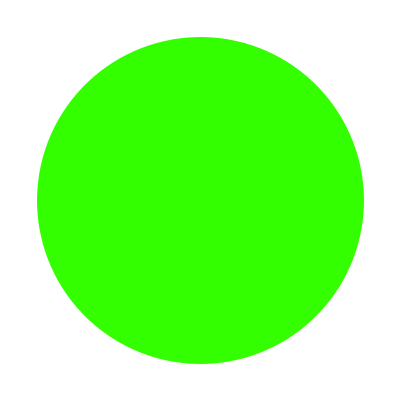
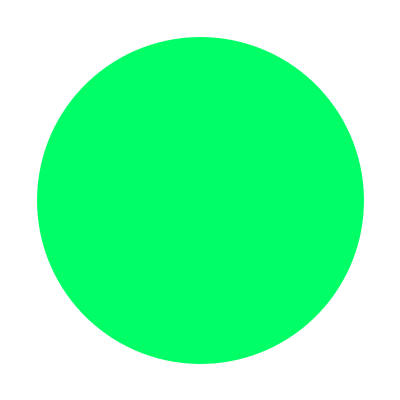
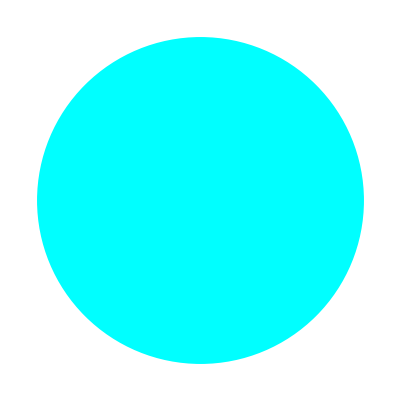
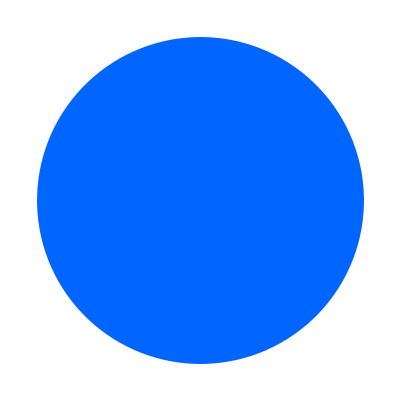
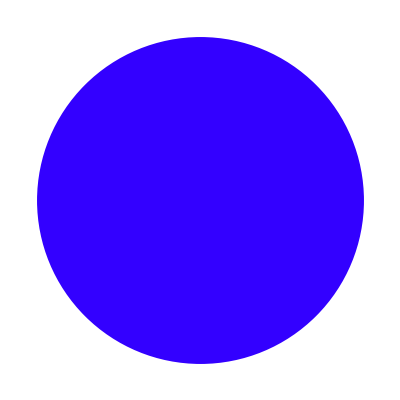
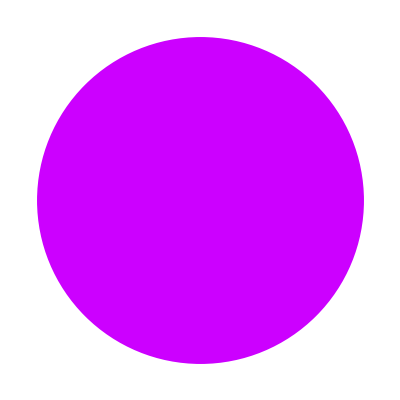
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graphics[Style[Disk[],Hue[#]]]&/@Range[0,1,.1]
```

```mathematica
Graphics[Style[Disk[],Hue[#]&/@Range[0,.2,.1]]]
```

-Graphics-

```mathematica
Hue[#]&/@Range[0,1,.1]
```

{Hue[0.],Hue[0.1],Hue[0.2],Hue[0.30000000000000004],Hue[0.4],Hue[0.5],Hue[0.6000000000000001],Hue[0.7000000000000001],Hue[0.8],Hue[0.9],Hue[1.]}

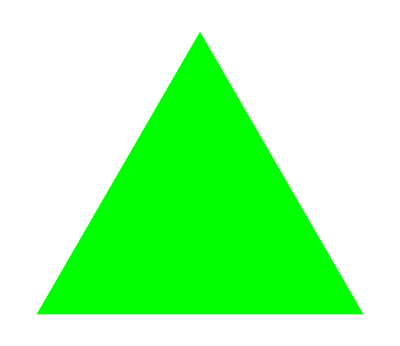
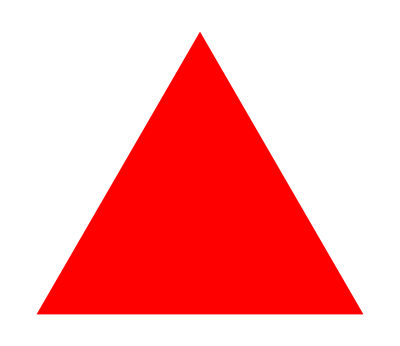

```mathematica
Column[{Join[Graphics[Style[RegularPolygon[3],Red]]
Graphics[Style[RegularPolygon[3],Green]]]}]
```

```mathematica
Graphics3D[Style[Cylinder[],Purple]]
```

-Graphics3D-

Table::nliter: Non-list iterator Reverse[{n,3,8}] at position 2 does not evaluate to a real numeric value.

```mathematica
Table[Graphics[RegularPolygon[n]],{n,5,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

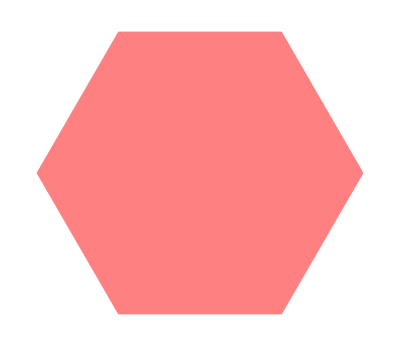
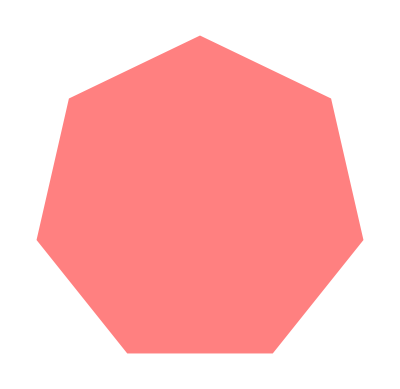
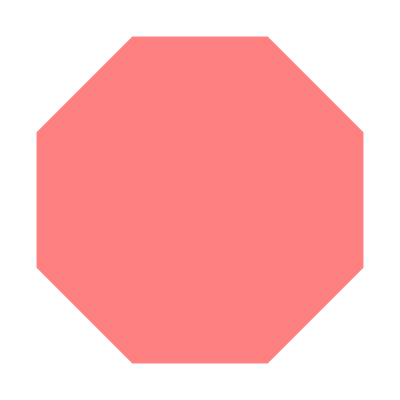
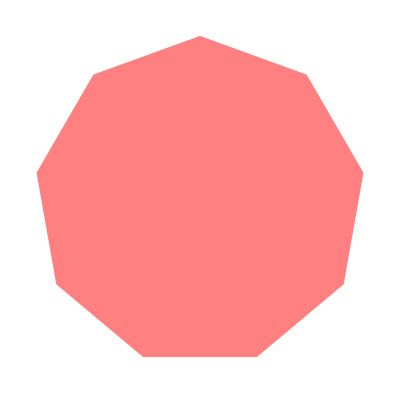
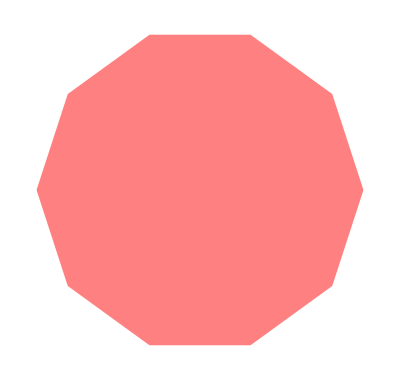
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[Style[RegularPolygon[n],Pink]],{n,5,10}]
```

```mathematica
Table[Graphics[RegularPolygon[10]],{10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

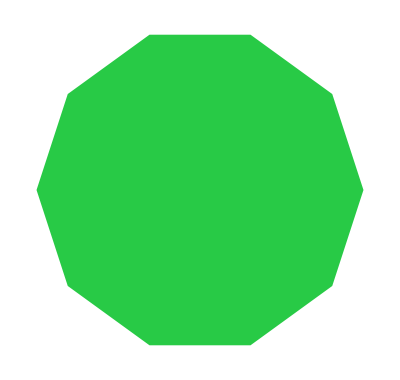

```mathematica
Graphics[Style[RegularPolygon[10],RandomColor[]]]
```